```mathematica
Exit[]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
diffPD1 = {cA''[x]== ((phiA^2)/(L^2))*cA[x],cA'[0]==0, cA[L]==a};
solPD1 = DSolve[diffPD1, cA[x],x]
```

{{cA[x]→(a ⅇ^(phiA-(phiA x)/L) (1+ⅇ^((2 phiA x)/L)))/(1+ⅇ^(2 phiA))}}

```mathematica
Sim1 = FullSimplify[solPD1]
```

{{cA[x]→a Cosh[(phiA x)/L] Sech[phiA]}}

```mathematica
diffPD2 = {cB''[x]==((+phiB^2)/(L^2))*cB[x]+ ((-phiA^2)/(L^2))*a*Cosh[(phiA x)/L]*Sech[phiA],cB'[0]==0, cB[L]==0}
solPD2= DSolve[diffPD2, cB[x],x]
```

{cB''[x]==(phiB^2 cB[x])/L^2-(a phiA^2 Cosh[(phiA x)/L] Sech[phiA])/L^2,cB'[0]==0,cB[L]==0}

{{cB[x]→-((a ⅇ^(-(phiB x)/L) phiA^2 (ⅇ^phiB+ⅇ^(phiB+(2 phiB x)/L)-ⅇ^((phiB x)/L) Cosh[(phiA x)/L] Sech[phiA]-ⅇ^(2 phiB+(phiB x)/L) Cosh[(phiA x)/L] Sech[phiA]))/((1+ⅇ^(2 phiB)) (-phiA+phiB) (phiA+phiB)))}}

```mathematica
Sim2 = FullSimplify[solPD2]
```

{{cB[x]→(a phiA^2 (-Cosh[(phiA x)/L] Sech[phiA]+Cosh[(phiB x)/L] Sech[phiB]))/(phiA^2-phiB^2)}}

```mathematica
L=0.05;
a =0.1;
kA= 2;
kB = 0.5;
Deff= 1.9*10^(-5);
phiA=L*(kA/Deff)^0.5;
phiB=L*(kB/Deff)^0.5;
```

```mathematica
L= 0.005;
a =0.1;
Deff= 1.9*10^(-5);
phiA=L*(kA/Deff)^0.5;
phiB=L*(kB/Deff)^0.5;
```

```mathematica
cAExpr=FullSimplify[cA[x]/. Sim1[[1]]];
cBExpr=FullSimplify[cB[x]/. Sim2[[1]]];
```

```mathematica
c=Integrate[kB*cBExpr,{x,0,L}];

d=Integrate[kA*cAExpr-kB*cBExpr,{x,0,L}];
```

```mathematica
Selectivity3 = c/d
```

(kB phiA^2 (phiB Tanh[phiA]-phiA Tanh[phiB]))/(phiB (-((kA+kB) phiA^2)+kA phiB^2) Tanh[phiA]+kB phiA^3 Tanh[phiB])

```mathematica
SimSelec = FullSimplify[Selectivity3]
```

(kB phiA^2 (phiB Tanh[phiA]-phiA Tanh[phiB]))/(phiB (-((kA+kB) phiA^2)+kA phiB^2) Tanh[phiA]+kB phiA^3 Tanh[phiB])

```mathematica
Selectivity4=c/d
```

(kB phiA^2 (phiB Tanh[phiA]-phiA Tanh[phiB]))/(phiB (-((kA+kB) phiA^2)+kA phiB^2) Tanh[phiA]+kB phiA^3 Tanh[phiB])

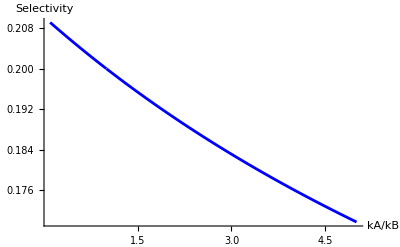

```mathematica
(*Define constants*)L=0.005;
a=0.1;
Deff=1.9*10^(-5);
kB=0.5;

(*Redefine phiA and phiB in terms of kA and kB*)
phiA[L_,kA_]:=L*Sqrt[kA/Deff];
phiB[L_,kB_]:=L*Sqrt[kB/Deff];

(*Simplified selectivity expression*)
SelectivityRatioExpr=FullSimplify[(kB phiA[L,r*kB]^2 (phiB[L,kB] Tanh[phiA[L,r*kB]]-phiA[L,r*kB] Tanh[phiB[L,kB]]))/(phiB[L,kB] (-((r*kB+kB) phiA[L,r*kB]^2)+r*kB phiB[L,kB]^2)*Tanh[phiA[L,r*kB]]+kB phiA[L,r*kB]^3 Tanh[phiB[L,kB]])];

(*Plot selectivity as a function of the ratio kA/kB*)
Plot[Evaluate[SelectivityRatioExpr],{r,0.1,5},PlotRange->All,AxesLabel->{"kA/kB","Selectivity"},PlotStyle->Blue,PlotLegends->"Expressions"]
```

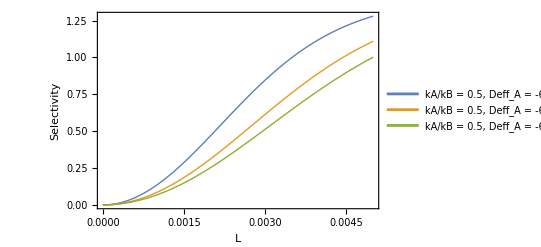

```mathematica
(*Constants*)Lmin=0.005;
Lmax=0.05;
a=0.1;
kB=0.5;

(*Ratios of kA/kB*)
ratios={0.5};

(*Effective diffusion coefficients for A*)
DeffValues={1.18*10^-6,1.9*10^-6,2.4*10^-6};


(*Expression for Selectivity with parameterized kA,L,and Deff_A*)
SelectivityWithL[kARatio_,DeffA_,L_]:=Module[{phiA,phiB,kA,Selectivity},kA=kARatio*kB;
phiA=L*Sqrt[kA/DeffA];
phiB=L*Sqrt[kB/DeffA];
Selectivity=(kB*phiA^2*(phiB*Tanh[phiA]-phiA*Tanh[phiB]))/(phiB*(-((kA+kB)*phiA^2)+kA*phiB^2)*Tanh[phiA]+kB*phiA^3*Tanh[phiB]);
Selectivity];

(*Plotting with adjusted L range and Quiet to suppress error messages*)
Quiet[Plot[Evaluate[Table[SelectivityWithL[r,Deff,L],{r,ratios},{phiA,}]],{L,0,0.005},PlotRange->All,AxesLabel->{"L","Selectivity"},PlotLegends->Placed[Flatten[Table["kA/kB = "<>ToString[r]<>", Deff_A = "<>ToString[Deff],{r,ratios},{Deff,DeffValues}]],Right],PlotStyle->Thick,Frame->True]]
```

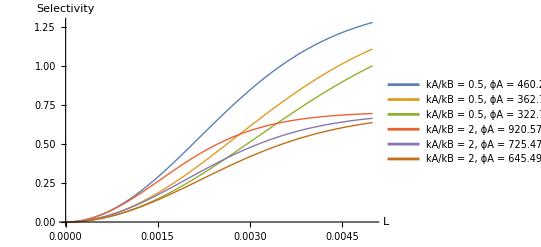

```mathematica
(*Constants*)Lmin=0.005;
Lmax=0.05;
a=0.1;
kB=0.5;

(*Ratios of kA/kB*)
ratios={0.5,2};

(*Effective diffusion coefficients for A and corresponding PhiA labels*)
DeffValues={1.18*10^-6,1.9*10^-6,2.4*10^-6};
phiALabels=Table[Sqrt[r*kB/Deff],{r,ratios},{Deff,DeffValues}];

(*Expression for Selectivity with parameterized kA,L,and Deff_A*)
SelectivityWithL[kARatio_,DeffA_,L_]:=Module[{phiA,phiB,kA,Selectivity},kA=kARatio*kB;
phiA=L*Sqrt[kA/DeffA];
phiB=L*Sqrt[kB/DeffA];
Selectivity=(kB*phiA^2*(phiB*Tanh[phiA]-phiA*Tanh[phiB]))/(phiB*(-((kA+kB)*phiA^2)+kA*phiB^2)*Tanh[phiA]+kB*phiA^3*Tanh[phiB]);
Selectivity];

(*Plotting with adjusted L range and Quiet to suppress error messages*)
Quiet[Plot[Evaluate[Table[SelectivityWithL[r,Deff,L],{r,ratios},{Deff,DeffValues}]],{L,0,0.005},PlotRange->All,AxesLabel->{"L","Selectivity"},Frame->False,FrameLabel->None,PlotLegends->Placed[Flatten[Table["kA/kB = "<>ToString[r]<>", ϕA = "<>ToString[N[Sqrt[r*kB/Deff],3]],{r,ratios},{Deff,DeffValues}]],Right],PlotStyle->Thick]]
```